```mathematica
Show[{Plot3D[{myFunction[x_,y_]=2+Sin[x +y/3]/10+Cos[y]/4,0},{x,0,10},{y,0,10},PlotRange->{0,3},ColorFunction->Black,PlotStyle->Opacity[0],Boxed->False,Axes->False,Mesh->None,ViewPoint->{0,1,2}],Graphics3D[{Line[{{0,0,0},{0,0,myFunction[0,0]}}],Line[{{10,0,0},{10,0,myFunction[10,0]}}],Line[{{0,10,0},{0,10,myFunction[0,10]}}],Line[{{10,10,0},{10,10,myFunction[10,10]}}],Line[{{0,0,0},{10,0,0}}],Line[{{0,0,0},{0,10,0}}],Line[{{10,0,0},{10,10,0}}],Line[{{0,10,0},{10,10,0}}],Arrow[BSplineCurve[{{4,10,0},{5,11,0},{4.5,13,0},{3.5,13,3},{3,11,3},{4,10,3}}]],Text[Style["Identified",16],{6,11.5,1}],Arrow[{{-1,0,-1},{3,0,-1}}],Arrow[{{-1,0,-1},{-1,4,-1}}],Arrow[{{-1,0,-1},{-1,0,2}}],Text[Style["x_0",16],{-1-1/2,2,-1}],Text[Style["x_1",16],{1,3/4,-1}],Text[Style["x_5",16],{-1-1/4,-1/2,2}]}]},PlotRange->All]
```

```mathematica
myFunction[x_,y_]:=2+Sin[x +y/3]/10+Cos[y]/4
```

```mathematica
Show[{Plot3D[2+Sin[x +y/3]/10+Cos[y]/4,{x,0,10},{y,0,10},PlotRange->{0,3},ColorFunction->Black,Boxed->False,Axes->False],Graphics3D[{Line[{{0,0,0},{0,0,myFunction[0,0]}}],Line[{{10,0,0},{10,0,myFunction[10,0]}}],Line[{{0,10,0},{0,10,myFunction[0,10]}}],Line[{{10,10,0},{10,10,myFunction[10,10]}}],Line[{{0,0,0},{10,0,0}}],Line[{{0,0,0},{0,10,0}}],Line[{{10,0,0},{10,10,0}}],
Line[{{0,10,0},{10,10,0}}],Arrow[{{-1,-1,0},{3,-1,0}}],Arrow[{{-1,-1,0},{-1,3,0}}],Arrow[{{-1,-1,0},{-1,-1,2}}],Text[Style["x_0",16],{-1-3/4,1,0}],Text[Style["x_1",16],{1/2,-1-1/2,0}],Text[Style["ϕ(x_0,x_1)",16],{-1,-3/4,2+1/4}]}]},PlotRange->All]
```

```mathematica
myX=RandomReal[{0,1},{200,1}];
myY=RandomReal[{0,4},{800,1}];
```

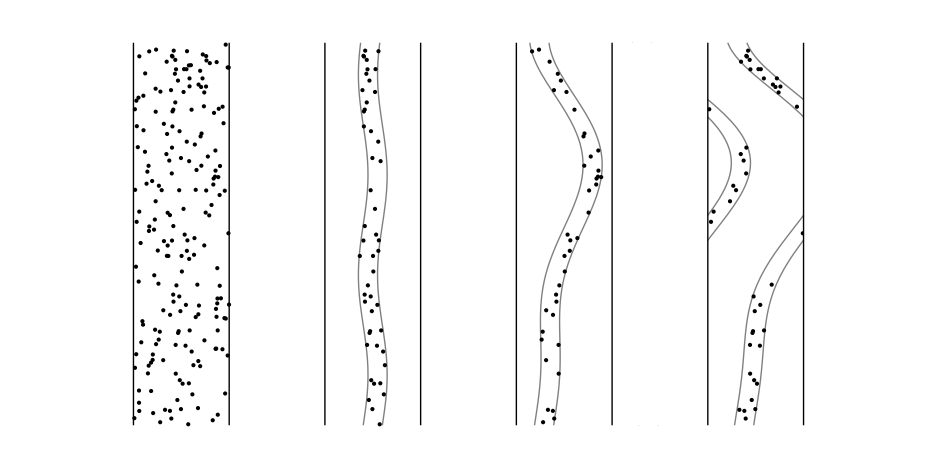

```mathematica
Show[{ParametricPlot[{{2+4/10+Sin[3t]/20,t},{2+6/10+Sin[3t]/20,t},{4+4/10+Sin[3t]/20+Sin[t^2/3-1]/4,t},{4+6/10+Sin[3t]/20+Sin[t^2/3-1]/4,t},{6+7/10+Sin[3t]/20+Sin[t^2/3-1]/2,t},{6+9/10+Sin[3t]/20+Sin[t^2/3-1]/2,t},{5+7/10+Sin[3t]/20+Sin[t^2/3-1]/2,t},{5+9/10+Sin[3t]/20+Sin[t^2/3-1]/2,t}},{t,0,4},PlotStyle->Gray,Axes->False],ListPlot[Table[{myX[[i]][[1]],myY[[i]][[1]]},{i,1,200}],PlotStyle->Black,Axes->False],ListPlot[Select[Table[{2+myX[[i]][[1]],myY[[i]][[1]]},{i,1,200}],First[#]>(2+4/10+Sin[3  Last[#]]/20)&&First[#]<(2+6/10+Sin[3  Last[#]]/20)&],PlotStyle->Black,Axes->False],ListPlot[Select[Table[{4+myX[[i]][[1]],myY[[i]][[1]]},{i,1,200}],First[#]>(4+4/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/4)&&First[#]<(4+6/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/4)&],PlotStyle->Black,Axes->False],ListPlot[Select[Table[{6+myX[[i]][[1]],myY[[i]][[1]]},{i,1,200}],First[#]>(6+7/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/2)&&First[#]<(6+9/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/2)||First[#]>(5+7/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/2)&&First[#]<(5+9/10+Sin[3Last[#]]/20+Sin[Last[#]^2/3-1]/2)&],PlotStyle->Black,Axes->False],Graphics[{{White,Rectangle[{-1/2,0},{0,4}],Rectangle[{5,0},{6,4}],Rectangle[{7,0},{7+1/2,4}]},Line[{{0,0},{0,4}}],Line[{{1,0},{1,4}}],Line[{{2,0},{2,4}}],Line[{{3,0},{3,4}}],Line[{{4,0},{4,4}}],Line[{{5,0},{5,4}}],Line[{{6,0},{6,4}}],Line[{{7,0},{7,4}}]}]},PlotRange->All]
```

```mathematica
myX=RandomReal[{0,1},{200,1}];
myY=RandomReal[{0,3},{800,1}];
```

```mathematica
myXY={{0.8929897421653199,1.4203732565433693},{0.34436964383444457,0.2470495625010507},{0.4231148045862452,2.151708719052329},{0.2911905734821627,2.4948887499401424},{0.22068269572931332,2.018233385192934},{0.0486091433569551,2.356788566082467},{0.5860519714491552,1.3},{0.005352030521428075,0.8947206245357817},{0.4845873675813219,0.9771840762186668},{0.64371388094359,2.183221817172768},{0.6505068147067279,0.5947964774890346},{0.6586285987752276,1.8608749329975183},{0.24705851255392286,1.753691727760259},{0.11763105532859242,2.1017631640503796},{0.043327411370921,0.8798257490552084},{0.8414355298652827,2.4293462180098793},{0.9617279184956675,2.32878235088629},{0.7388502343646997,1.6833596625075344},{0.1,0.3},{0.95,0.6},{0.3,1.1},{0.7,0.9},{0.2,1.4}};
```

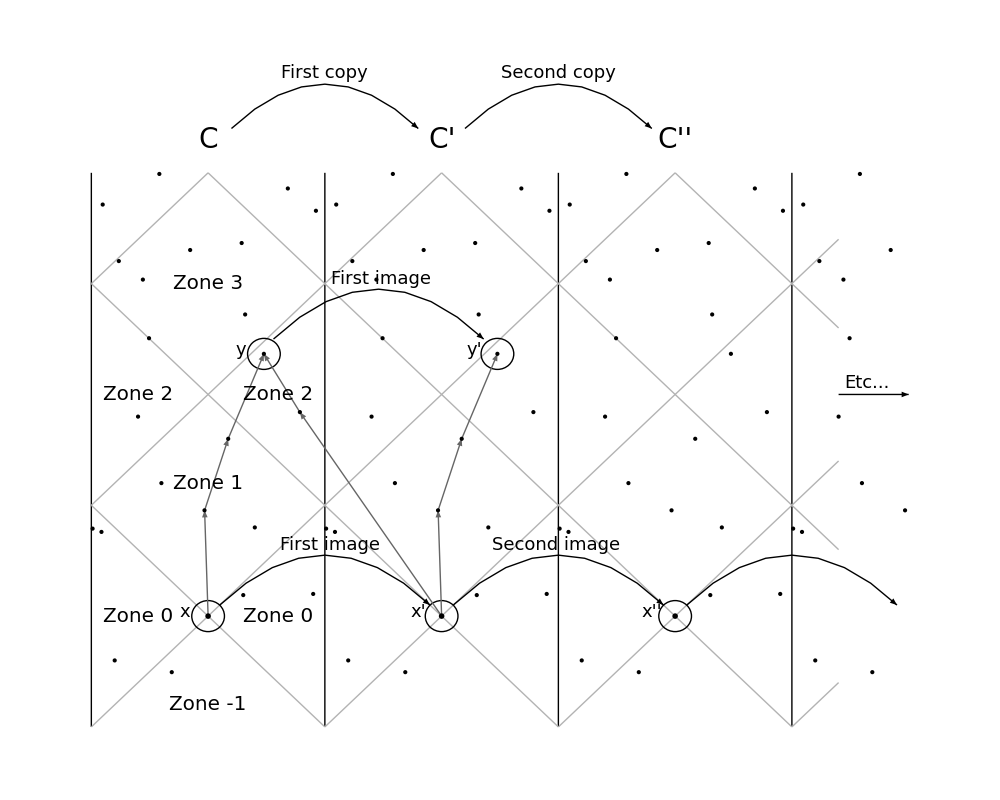

```mathematica
Show[{Graphics[{Line[{{0,0},{0,2.5}}],Line[{{1,0},{1,2.5}}],Line[{{2,0},{2,2.5}}],Line[{{3,0},{3,2.5}}],{GrayLevel[.7],Line[{{0,2},{.5,2.5}}],Line[{{0,1},{1.5,2.5}}],Line[{{0,0},{2.5,2.5}}],Line[{{1,0},{3.2,2.2}}],Line[{{2,0},{3.2,1.2}}],Line[{{3,0},{3.2,0.2}}],Line[{{1,0},{0,1}}],Line[{{2,0},{0,2}}],Line[{{3,0},{.5,2.5}}],Line[{{3.2,0.8},{1.5,2.5}}],Line[{{3.2,1.8},{2.5,2.5}}]},{Arrowheads[0.02],Arrow[BezierCurve[{{.55,.55},{1,1},{1.45,.55}}]],Arrow[BezierCurve[{{1.55,.55},{2,1},{2.45,.55}}]],Arrow[BezierCurve[{{2.55,.55},{3,1},{3.45,.55}}]],Arrow[BezierCurve[{{.78,1.75},{1.23,2.2},{1.68,1.75}}]],Arrow[BezierCurve[{{.6,2.7},{1,3.1},{1.4,2.7}}]],Arrow[BezierCurve[{{1.6,2.7},{2,3.1},{2.4,2.7}}]],Arrow[{{3.2,1+1/2},{3.5,1+1/2}}]},Circle[{1/2,1/2},.07],Circle[{1+1/2,1/2},.07],Circle[{2+1/2,1/2},.07],Circle[{0.739,1.683},.07],Circle[{1.739,1.683},.07],{Arrowheads[0.01],GrayLevel[.4],Arrow[{{.5,.5},{.485,.977}}],Arrow[{{.485,.977},{.586,1.3}}],Arrow[{{.586,1.3},{.739,1.683}}],Arrow[{{1.5,.5},{1.485,.977}}],Arrow[{{1.485,.977},{1.586,1.3}}],Arrow[{{1.586,1.3},{1.739,1.683}}],Arrow[{{1.5,.5},{.893,1.42}}],Arrow[{{.893,1.42},{.739,1.683}}]},Text[Style["C",Italic,28],{.5,2.65}],Text[Style["C'",Italic,28],{1.5,2.65}],Text[Style["C''",Italic,28],{2.5,2.65}],Text[Style["y",18],{.64,1.7}],Text[Style["y'",18],{1.64,1.7}],Text[Style["x",18],{.4,.52}],Text[Style["x'",18],{1.4,.52}],Text[Style["x''",18],{2.4,.52}],Text[Style["First copy",18],{1,2.95}],Text[Style["Second copy",18],{2,2.95}],Text[Style["First image",18],{1.02,.82}],Text[Style["Second image",18],{1.99,.82}],Text[Style["First image",18],{1.24,2.02}],Text[Style["Etc...",18],{3.32,1.55}],Text[Style["Zone -1",Italic,20],{1/2,.1}],Text[Style["Zone 0",Italic,20],{.2,1/2}],Text[Style["Zone 0",Italic,20],{.8,1/2}],Text[Style["Zone 1",Italic,20],{.5,1.1}],Text[Style["Zone 2",Italic,20],{.2,1.5}],Text[Style["Zone 2",Italic,20],{.8,1.5}],Text[Style["Zone 3",Italic,20],{.5,2}]}],ListPlot[myXY,PlotStyle->Black,Axes->False],ListPlot[Table[{1+myXY[[i]][[1]],myXY[[i]][[2]]},{i,1,Length[myXY]}],PlotStyle->Black,Axes->False],ListPlot[Table[{2+myXY[[i]][[1]],myXY[[i]][[2]]},{i,1,Length[myXY]}],PlotStyle->Black,Axes->False],ListPlot[Select[Table[{3+myXY[[i]][[1]],myXY[[i]][[2]]},{i,1,Length[myXY]}],First[#]<3+1/2&],PlotStyle->Black,Axes->False],
ListPlot[{{1/2,1/2},{1+1/2,1/2},{2+1/2,1/2}},PlotStyle->{Black,PointSize->.004},Axes->False]},PlotRange->All,AspectRatio->4/5,ImageSize->1000]
```

```mathematica
x≺y≺z ⟹ x≺z
x≺y and y≺x ⟹ x=y
[x,y]<∞

N ⟷ V
x≺y ⟷ x∈SuperMinus[J](y)
```

```mathematica
S=- 1/(16π G̃)∫d^5 x √(|g|)R̃
```

```mathematica
S=- (2π ϕ)/(16π G̃)∫d^4 x √(|g|)(R+1/4 ϕ Subscript[F, μν] F^μν)
```

```mathematica
Subscript[F, μν]= D[Subscript[A, ν], μ]-D[Subscript[A, μ], ν]
```

```mathematica
G̃=2π G ?ϕ?
```

```mathematica
({{g+ϕ A A, ϕ A}, {ϕ A, ϕ}})
```

```mathematica
ψ(x⃗, Subscript[x, 5])=∑_(n=-∞)^∞ ψ^(n)e^(in Subscript[x, 5]/r)
```

f_r(i,j) | = | -CK^2/∥x_i-x_j∥, i≠j, i,j∈V
f_a(i,j) | = | ∥x_i-x_j∥^2/K, i↔j.

f(i,x,K,C)=∑_(i≠j) (-C K^2)/(∥x_i-x_j∥^2)(x_j-x_i)+∑_(i↔j) (∥x_i-x_j∥)/K(x_j-x_i).

f(i,x,K,C) | = | ∑_(i≠j) (-C K^2)/(∥x_i-x_j∥^2)(x_j-x_i)+∑_(i↔j) (∥x_i-x_j∥)/K(x_j-x_i)
  | = | (C/C')^(2/3)K/K'(∑_(i≠j) (-C'(K')^2)/(∥s x_i-s x_j∥^2)(s x_j-s x_i)+∑_(i↔j) (∥s x_i-s x_j∥)/K'(s x_j-s x_i))
  | = | (C/C')^(2/3)K/K' f(i,s x,K',C'),

Energy_se(x,K,C)=(C/C')^(4/3)(K/K')^2 Energy_se(s x,K',C').

f_r(i,j)=-CK^(1+p)/∥x_i-x_j∥^p, i≠j, i,j∈V, p>0.

f_r(i,j)=f_a(i,j)=∥x_i-x_j∥-d(i,j), i≠j, i,j∈V